# Bifurcación de tridente supercrítico

## Forma normal:

### Espacio fase

```mathematica
Manipulate[Plot[r*x-x^3,{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{{-2,2},{-10,10}},AspectRatio->1],{r,-2,2}]
```

### Soluciones antes del punto crítico y en el punto crítico

```mathematica
sol1=NDSolve[{x'[t]==-2*x[t]-x[t]^3,x[0]==1},x,{t,0,10}]
sol2=NDSolve[{x'[t]==-x[t]^3,x[0]==1},x,{t,0,10}]
```

{{x→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…]}}

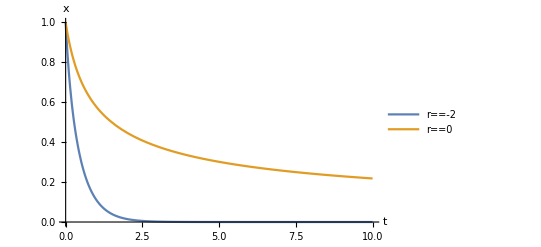

```mathematica
psol1=Plot[{Evaluate[x[t]/.sol1],Evaluate[x[t]/.sol2]},{t,0,10},AxesLabel->{t,x},PlotLegends->{r==-2,r==0}]
```

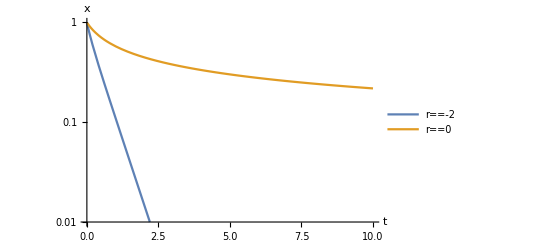

```mathematica
psol2=LogPlot[{Evaluate[x[t]/.sol1],Evaluate[x[t]/.sol2]},{t,0,10},AxesLabel->{t,x},PlotLegends->{r==-2,r==0},PlotRange->{{0,10},{0.01,1}}]
```

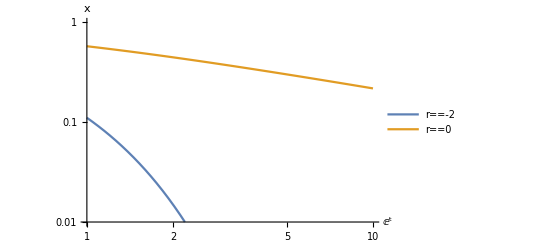

```mathematica
psol3=LogLogPlot[{Evaluate[x[t]/.sol1],Evaluate[x[t]/.sol2]},{t,1,10},AxesLabel->{t,x},PlotLegends->{r==-2,r==0},PlotRange->{{1,10},{0.01,1}}]
```

### Diagrama de bifurcación

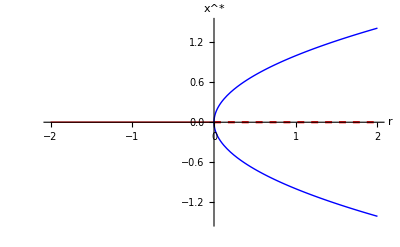

```mathematica
bdiag=Show[Plot[0,{r,-2,0},PlotStyle->{Red,Thick},PlotRange->{{-2,2},{-3/2,3/2}},AxesLabel->{r,SuperStar[x]}],Plot[0,{r,0,2},PlotStyle->{Red,Dashed},PlotRange->{{-2,2},{-3/2,3/2}},AxesLabel->{r,SuperStar[x]}],Plot[Sqrt[r],{r,0,2},PlotStyle->{Blue,Thick},PlotRange->{{-2,2},{-3/2,3/2}},AxesLabel->{r,SuperStar[x]}],Plot[-Sqrt[r],{r,0,2},PlotStyle->{Blue,Thick},PlotRange->{{-2,2},{-3/2,3/2}},AxesLabel->{r,SuperStar[x]}]]
```

## Ejercicio:

```mathematica
Series[x-b*Tanh[x],{x,0,3}]
```

(1-b) x+(b x^3)/3+O[x]^4

```mathematica
solex11=ParallelTable[{b,x/.FindRoot[x==b*Tanh[x],{x,b}]},{b,1,4,0.01}];
solex12=ParallelTable[{b,x/.FindRoot[x==b*Tanh[x],{x,-b}]},{b,1,4,0.01}];
```

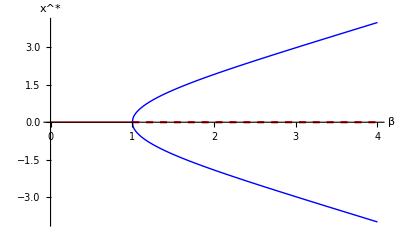

```mathematica
bdex1=Show[Plot[0,{r,0,1},PlotStyle->{Red,Thick},PlotRange->{{0,4},{-4,4}},AxesLabel->{β,SuperStar[x]}],Plot[0,{r,1,4},PlotStyle->{Red,Dashed},PlotRange->{{0,4},{-4,4}},AxesLabel->{β,SuperStar[x]}],ListPlot[solex11,Joined->True,PlotStyle->{Blue,Thick},PlotRange->{{0,4},{-4,4}},AxesLabel->{β,SuperStar[x]}],ListPlot[solex12,Joined->True,PlotStyle->{Blue,Thick},PlotRange->{{0,4},{-4,4}},AxesLabel->{β,SuperStar[x]}]]
```